# Boundary Conditions

```mathematica
MakeBoxes[ap,TraditionalForm]:="a_+";
MakeBoxes[am,TraditionalForm]:="a_-";
MakeBoxes[ep,TraditionalForm]:="e_-";
MakeBoxes[em,TraditionalForm]:="e_-";
MakeBoxes[vp,TraditionalForm]:="v_+";
MakeBoxes[vm,TraditionalForm]:="v_-";
MakeBoxes[wp,TraditionalForm]:="w_+";
MakeBoxes[wm,TraditionalForm]:="w_-";
MakeBoxes[γp,TraditionalForm]:="γ_+";
MakeBoxes[γm,TraditionalForm]:="γ_-";
MakeBoxes[pp,TraditionalForm]:="p_+";
MakeBoxes[pm,TraditionalForm]:="p_-";
MakeBoxes[Tp,TraditionalForm]:="T_+";
MakeBoxes[Tm,TraditionalForm]:="T_-";
MakeBoxes[αp,TraditionalForm]:="α_+";
MakeBoxes[αm,TraditionalForm]:="α_-";
MakeBoxes[ϵp,TraditionalForm]:="ϵ_+";
MakeBoxes[ϵm,TraditionalForm]:="ϵ_-";
```

```mathematica
$Assumptions={};
```

```mathematica
eqns={vp vm ==(1-(1-3αp)r)/(3-3(1+αp)r),vp/vm==(3+(1-3αp)r)/(1+3(1+αp)r)};
eqns/.{αp->(ϵp-ϵm)/(ap Tp^4),r->(ap Tp^4)/(am Tm^4)}/.{ap->-3/(4 Tp^3)D[Veff[T],T]/.{T->Tp},am->-3/(4 Tm^3)D[Veff[T],T]/.{T->Tm},ϵp->(Veff[Tp]+-Tp/4 D[Veff[T],T]/.{T->Tp}),ϵm->(Veff[Tm]+-Tm/4 D[Veff[T],T]/.{T->Tm})}//Simplify
eqnbag=eqns/.{αp->ϵ/(ap Tp^4),r->(ap Tp^4)/(am Tm^4)}//Simplify (*Assuming perfect bag model*)
```

{v_- v_+==(Veff(T_-)-Veff(T_+))/(T_- Veff'(T_-)-Veff(T_-)-T_+ Veff'(T_+)+Veff(T_+)),(v_+)/(v_-)==(T_- Veff'(T_-)-Veff(T_-)+Veff(T_+))/(Veff(T_-)+T_+ Veff'(T_+)-Veff(T_+))}

{v_- v_+==(a_- (T_-)^4-a_+ (T_+)^4+3 ϵ)/(3 a_- (T_-)^4-3 (a_+ (T_+)^4+ϵ)),(v_+)/(v_-)==(3 a_- (T_-)^4+a_+ (T_+)^4-3 ϵ)/(a_- (T_-)^4+3 a_+ (T_+)^4+3 ϵ)}

```mathematica
eqnbag[[1]]
```

v_- v_+==(a_- (T_-)^4-a_+ (T_+)^4+3 ϵ)/(3 a_- (T_-)^4-3 (a_+ (T_+)^4+ϵ))

```mathematica
num={Tn->53.31938236527749,ap->35.12,am->33.1,ϵp->9460721.320042096,ϵm->0,ϵ->9460721.320042096}(*Bag Model*);
```

```mathematica
(3+(1-3αp)r)/(1+3(1+αp)r)/.{αp->(ϵp-ϵm)/(ap Tp^4),r->(ap Tp^4)/(am Tm^4)}/.num/.{Tp->80,vp->0.7}/.{Tm->81}//Simplify
```

0.895764

## Try to solve the boundary equations in the perfect bag model

First test the SM case with arbitrary parameter.

### Detonation

```mathematica
NSolve[(eqnbag/.num/.{vp->0.7,Tp->80,ϵ->10^7}),{vm,Tm},PositiveReals]
```

{{v_-→0.694703,T_-→82.5502},{v_-→0.479822,T_-→100.008}}

```mathematica
sol=NSolve[(eqnbag/.num/.{vp->0.7,Tp->80,ϵ->10^7}),{vm,Tm},PositiveReals][[1]];
```

```mathematica
h[z_]:=1/2(1-Tanh[z]);
```

```mathematica
Solve[h[]]
```

### Deflagration

```mathematica
μ[x_,v_]=(x-v)/(1-x v);
```

```mathematica
Deqns={2 v[x]/x==1/(1-v[x]^2)(1-v[x]x)(μ[x,v[x]]^2/(1/3)-1)v'[x],T'[x]==T[x] 1/(1-v[x]^2)μ[x,v[x]] v'[x]};
```

Try to solve: v_w=0.5. Remember in deflagration we have v_->v_+.

```mathematica
vw=0.5;
sol=NSolve[(eqnbag/.num/.{vm->vw,Tm->53}),{vp,Tp},PositiveReals][[1]]
```

{v_+→0.412062,T_+→56.2182}

We should first solve the velocity profile. Use energy budget paper Eq 33.

```mathematica
{vsol[τ_],ξsol[τ_]}={v[τ],ξ[τ]}/.NDSolve[{v'[τ]==2 v[τ] 1/3(1-v[τ]^2)(1-ξ[τ]v[τ]),ξ'[τ]==ξ[τ]((ξ[τ]-v[τ])^2-1/3(1-ξ[τ]v[τ])^2),(ξ[10]==vw),v[10]==μ[vw,vp]/.sol},{v[τ],ξ[τ]},{τ,0.01,10}][[1]]
```

{InterpolatingFunction[…](τ),InterpolatingFunction[…](τ)}

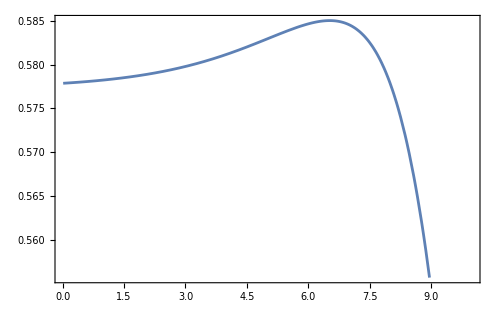

```mathematica
Plot[ξsol[x],{x,0.01,10}]
```

The ξ here is not a monotonic function as shown in energy budget paper in Fig.2. This is exactly the reason why we should not solve v as a function of ξ directly: ξ has a maximum. We should find the maximum at first.

```mathematica
τmin=x/.FindMaximum[ξsol[x],{x,6.69}][[2]]
ξmax=FindMaximum[ξsol[x],{x,6.69}][[1]]
```

InterpolatingFunction::dmval: Input value {-70.21} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

6.52595

InterpolatingFunction::dmval: Input value {-70.21} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.585054

I don’t know why output so many warnings. Actually nothing is outside the solution region...

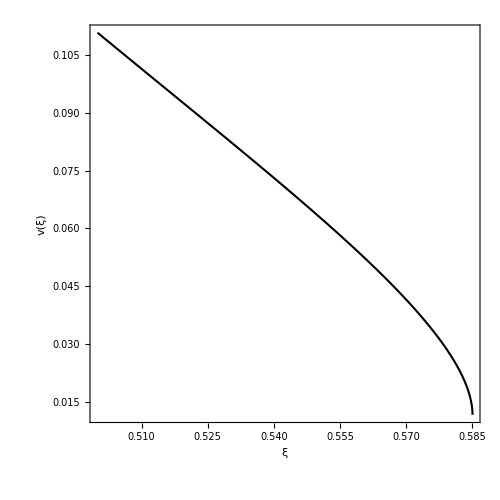

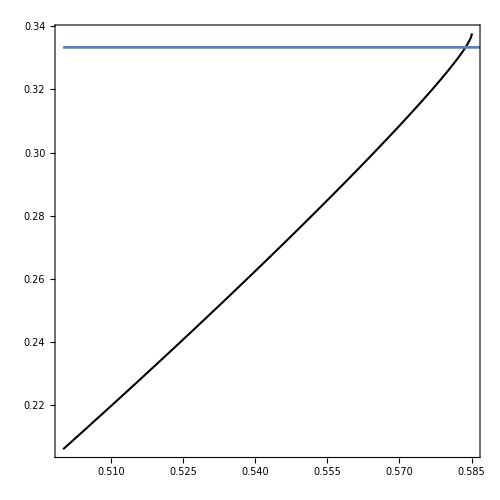

```mathematica
ParametricPlot[{ξsol[τ],vsol[τ]},{τ,τmin,10},AspectRatio->1,PlotRange->Full,FrameLabel->{"ξ","v(ξ)"}]
Show[ParametricPlot[{ξsol[τ],μ[ξsol[τ],vsol[τ]]ξsol[τ]},{τ,τmin,10},AspectRatio->1,PlotRange->Full],Plot[1/3,{x,0.5,0.7}]]
```

Now we have the maximum of ξ. Solve in this range.

```mathematica
{Tsol[x_],vsol[x_]}={T[x],v[x]}/.NDSolve[Join[Deqns,{(v[vw]==μ[0.5,vp]/.sol),(T[vw]==Tp/.sol)}],{T[x],v[x]},{x,vw,ξmax*0.9999}][[1]]
```

{InterpolatingFunction[…](x),InterpolatingFunction[…](x)}

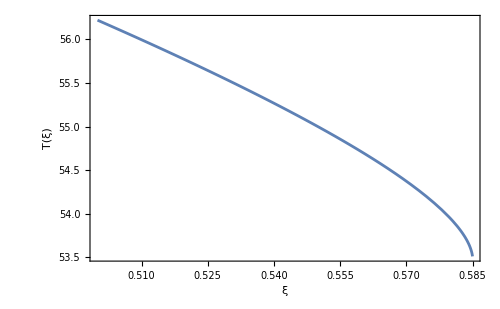

```mathematica
Plot[Tsol[x],{x,0.5,ξmax*0.9999},FrameLabel->{"ξ","T(ξ)"}]
```

Find the shock front.

```mathematica
xsh=x/.FindRoot[μ[x,vsol[x]]x==1/3,{x,0.55}]
```

InterpolatingFunction::dmval: Input value {0.587211} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.586829} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {0.586492} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.583731

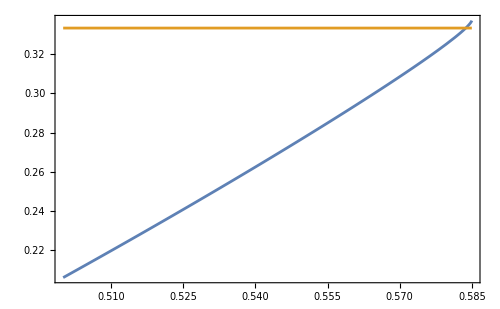

```mathematica
Plot[{μ[x,vsol[x]]x,1/3},{x,0.5,ξmax*0.9999}]
```

The temperature at the shock wave front should be

```mathematica
Tsol[xsh]
```

53.6955

```mathematica
find‵Tsh[Tmnum_,vw_]:=Block[{sol,vsol,ξsol,τmin,ξmax,Tsol,vsol2,Tveq,dsol,xsh},
sol=Select[{vp,Tp}/.NSolve[(eqnbag/.num/.{vm->vw,Tm->Tmnum}),{vp,Tp},PositiveReals],#[[1]]<1/(√3)&][[1]];
{vsol[τ_],ξsol[τ_]}={v[τ],ξ[τ]}/.NDSolve[{v'[τ]==2 v[τ] 1/3(1-v[τ]^2)(1-ξ[τ]v[τ]),ξ'[τ]==ξ[τ]((ξ[τ]-v[τ])^2-1/3(1-ξ[τ]v[τ])^2),(ξ[10]==vw),v[10]==μ[vw,sol[[1]]]},{v[τ],ξ[τ]},{τ,0.01,10}][[1]];
τmin=x/.FindMaximum[ξsol[x],{x,6.69}][[2]];
ξmax=FindMaximum[ξsol[x],{x,6.69}][[1]];
Tveq=Join[Deqns,{(v[vw]==μ[vw,sol[[1]]]),(T[vw]==sol[[2]])}];
dsol=(NDSolve[Tveq,{T[x],v[x]},{x,vw,ξmax*0.9999}][[1]]);
{Tsol[x_],vsol2[x_]}={T[x],v[x]}/.dsol;
xsh=x/.FindRoot[μ[x,vsol[x]]x==1/3,{x,0.55}];
Return[Tsol[xsh]]
]
```

```mathematica
find‵Tsh[53,0.5]
```

InterpolatingFunction::dmval: Input value {-70.21} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

54.0737

```mathematica
Tmax=53.32;
Tmin=50;
For[i=0,i<30,i++,
Tcalculate=(Tmax+Tmin)/2;
Tsh=find‵Tsh[Tcalculate,0.5];
If[Tsh<53.31938236527749,Tmin=Tcalculate,Tmax=Tcalculate];
]
```

InterpolatingFunction::dmval: Input value {-70.21} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

```mathematica
Tcalculate//N
```

52.1199

```mathematica
find‵Tsh[Tcalculate,0.5]
```

InterpolatingFunction::dmval: Input value {-70.21} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

53.3194

```mathematica
find‵Tm[vw_]:=Block[{Tmax,Tmin,Tcalculate,Tsh},
Tmax=53.32;
Tmin=50;
For[i=0,i<30,i++,
Tcalculate=(Tmax+Tmin)/2;
Tsh=find‵Tsh[Tcalculate,vw];
If[Tsh<53.31938236527749,Tmin=Tcalculate,Tmax=Tcalculate];
];
Return[Tcalculate]
]
```

```mathematica
find‵Tm[0.5]
```

InterpolatingFunction::dmval: Input value {-70.21} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

52.1199

```mathematica
find‵Tm[0.3]
```

InterpolatingFunction::dmval: Input value {-70.21} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaximum::sdprec will be suppressed during this calculation.

52.9605

```mathematica
find‵ΔS[vw_]:=Block[{Tmnum,vm,sol,vp,Tp},
Tmnum=find‵Tm[vw];
vm=vw;
sol=Select[{vp,Tp}/.NSolve[(eqnbag/.num/.{vm->vw,Tm->Tmnum}),{vp,Tp},PositiveReals],#[[1]]<1/(√3)&][[1]];
vp=sol[[1]];
Tp=sol[[2]];
Return[Tmnum/(√(1-vm^2))-Tp/(√(1-vp^2))]
]
```

```mathematica
find‵ΔS[0.1]
```

InterpolatingFunction::dmval: Input value {-0.334374} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaximum::sdprec will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-9.08889×10^15} and/or the interpolation grid is insufficient to compute the value.

FindMaximum::nrnum: The function value -InterpolatingFunction[(0.01 | 10.),{5,7,1,{69},{4},0,0,0,0,Automatic,«3»},(0.01 | 0.243879 | 0.477758 | 0.77916 | 1.08056 | 1.26573 | 1.4509 | 1.63607 | 1.82124 | 2.0064 | «59»),{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«60»},{0.565863,-0.00743685,0.56399,-0.0086067,0.561824,-0.00994468,0.558533,-0.0119473,0.554587,-0.014301,«128»}},{Automatic}][-9.08889×10^15] is not a real number at {x} = {-9.08889×10^15}.

InterpolatingFunction::dprec: The precision of input value {-9.08889×10^15} and/or the interpolation grid is insufficient to compute the value.

FindMaximum::nrnum: The function value -InterpolatingFunction[(0.01 | 10.),{5,7,1,{69},{4},0,0,0,0,Automatic,«3»},(0.01 | 0.243879 | 0.477758 | 0.77916 | 1.08056 | 1.26573 | 1.4509 | 1.63607 | 1.82124 | 2.0064 | «59»),{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«60»},{0.565863,-0.00743685,0.56399,-0.0086067,0.561824,-0.00994468,0.558533,-0.0119473,0.554587,-0.014301,«128»}},{Automatic}][-9.08889×10^15] is not a real number at {x} = {-9.08889×10^15}.

-0.607386

```mathematica
list=Table[{vw,find‵ΔS[vw]},{vw,0.1,0.55,0.05}];
```

InterpolatingFunction::dmval: Input value {-0.334374} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

General::stop: Further output of FindMaximum::sdprec will be suppressed during this calculation.

InterpolatingFunction::dprec: The precision of input value {-9.08889×10^15} and/or the interpolation grid is insufficient to compute the value.

FindMaximum::nrnum: The function value -InterpolatingFunction[(0.01 | 10.),{5,7,1,{69},{4},0,0,0,0,Automatic,«3»},(0.01 | 0.243879 | 0.477758 | 0.77916 | 1.08056 | 1.26573 | 1.4509 | 1.63607 | 1.82124 | 2.0064 | «59»),{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«60»},{0.565863,-0.00743685,0.56399,-0.0086067,0.561824,-0.00994468,0.558533,-0.0119473,0.554587,-0.014301,«128»}},{Automatic}][-9.08889×10^15] is not a real number at {x} = {-9.08889×10^15}.

InterpolatingFunction::dprec: The precision of input value {-9.08889×10^15} and/or the interpolation grid is insufficient to compute the value.

FindMaximum::nrnum: The function value -InterpolatingFunction[(0.01 | 10.),{5,7,1,{69},{4},0,0,0,0,Automatic,«3»},(0.01 | 0.243879 | 0.477758 | 0.77916 | 1.08056 | 1.26573 | 1.4509 | 1.63607 | 1.82124 | 2.0064 | «59»),{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«60»},{0.565863,-0.00743685,0.56399,-0.0086067,0.561824,-0.00994468,0.558533,-0.0119473,0.554587,-0.014301,«128»}},{Automatic}][-9.08889×10^15] is not a real number at {x} = {-9.08889×10^15}.

InterpolatingFunction::dprec: The precision of input value {-9.28981×10^15} and/or the interpolation grid is insufficient to compute the value.

General::stop: Further output of InterpolatingFunction::dprec will be suppressed during this calculation.

FindMaximum::nrnum: The function value -InterpolatingFunction[(0.01 | 10.),{5,7,1,{52},{4},0,0,0,0,Automatic,«3»},(0.01 | 0.336272 | 0.662545 | 1.05309 | 1.44364 | 1.77141 | 2.09918 | 2.42695 | 2.75472 | 3.0825 | «42»),{Developer`PackedArrayForm,{0,2,4,6,8,10,12,14,16,18,«43»},{0.575956,-0.000943069,0.575611,-0.00117462,0.575183,-0.00146237,0.57453,-0.00189949,0.573683,-0.00246474,«94»}},{Automatic}][-9.28981×10^15] is not a real number at {x} = {-9.28981×10^15}.

General::stop: Further output of FindMaximum::nrnum will be suppressed during this calculation.

NDSolve::ndsz: At x == 0.57735, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMaximum::lstol will be suppressed during this calculation.

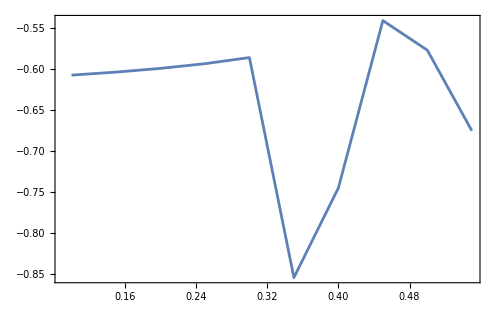

```mathematica
ListLinePlot[list]
```